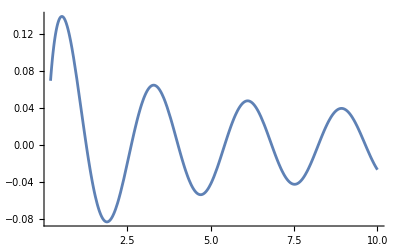

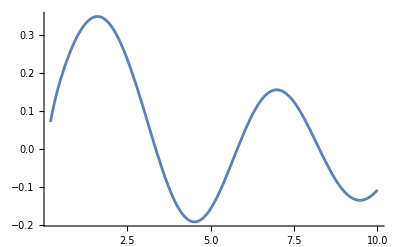

{InterpolatingFunction[…][r]}

{InterpolatingFunction[…][r]}

{(InterpolatingFunction[…][r])/(InterpolatingFunction[…][r])}

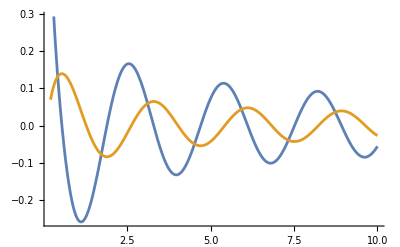

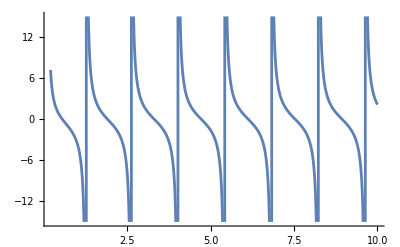

-Graphics-

{2.05714}

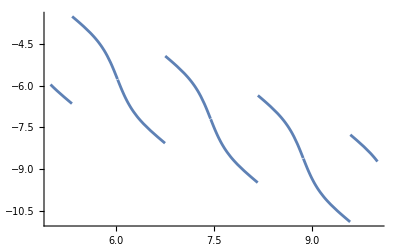

```mathematica
(* Upper Limit for integration *)
limit = 10;

(* Reduced Mass *)
μ=1835;
Subscript[m, p]=1836;
hbar= 1;  
c=137 ;(*SpeedOfLight, atomic units*)
 
vSg1Data = Import["~/Work/Physics-Thesis/thesis-2/MathematicaCode/sg1.mx"];
vSg2Data = Import["~/Work/Physics-Thesis/thesis-2/MathematicaCode/sg2.mx"];

maxR = 10;


(* Wave function outside scatterin region *)
psiRemote[r_,m_]:=(1/(√r)Cos[r-Pi(m+1/2)+delta]);
(* potential in the scattering region *)
vGerade:=Interpolation[Transpose[{vSg1Data[[All,1]],vSg1Data[[All,5]]}]];
vUngerade :=Interpolation[Transpose[{vSg2Data[[All,1]],vSg2Data[[All,5]]}]];

(* Wave function in the scatterin region *)
m=0;
k = 1;
geradeSol = 
NDSolve[{1/r D[r D [psiG[r],r],r]+(k^2-2vGerade[r]-m^2/r^2)psiG[r]==0,psiG[0.1] ==0,psiG'[0.1]==1},psiG[r],{r,0.1,10}];
unGeradeSol = 
First[NDSolve[{1/r D[r D [psiU[r],r],r]+(k^2-2vUngerade[r]-m^2/r^2)psiU[r]==0,psiU[0.1] ==0,psiU'[0.1]==1},psiU[r],{r,0.1,10}]];

Plot[psiG[r] /. geradeSol, {r,0.2,10}]

Plot[psiU[r] /. unGeradeSol, {r,0.2,10}]



(* Logarithmic derivative of the solution in the far region *)
fRemoteD[r_,k_,m]:=-1/(2r)-k Tan[k r - (m+1/2)/2+delta];
(* Logarithmic derivative of the solution in the scattering region *)
(*fGeradeD:=D[psiG[r] ,r]/(psiG[r] /. geradeSol );*)


fGeradeD=D[psiG[r]/.geradeSol,r];

logfGeradeD =D[psiG[r]/.geradeSol,r]/(psiG[r]/.geradeSol);

psiG[r]/.geradeSol

fGeradeD

logfGeradeD

Plot[{fGeradeD,psiG[r]/.geradeSol}, {r,0.2,10}]

Plot[{fGeradeD/psiG[r]/.geradeSol}, {r,0.2,10}]

Plot[logfGeradeD, {r,0.2,10}]

R = 10;
logfGeradeD /. r->R
(* logfGeradeD[r] == fRemoteD[r,k,m]*)
m = 0;

deltaG[x_, k_]:=ArcTan[(logfGeradeD /. r->x +1/(2x))/k]-k x +(m+1/2)/2;

Plot[deltaG[x,1], {x,5,10}]
```